## Hopping rates for C Frenkel defect in ZrC at the melting point

```mathematica
Data;

alatts={4.685,4.73,4.759,4.801,4.85};
SPE0={-.67203973*10^03,-.67129694*10^03,-.67034370*10^03,-.66835536*10^3,-.66520504*10^03};
SPperfectE0={-.67542431*10^03,-.67434729*10^03,-.67317107*10^03,-.67084734*10^03,-.66728258*10^03};
Esol=1000*(SPE0-SPperfectE0)//N;
fullrelaxlatt=9.37000000000000*{{0.9973148998093916,-0.0011864975152721, 0.0011864984262989},
{-0.0011873093032045 ,0.9970836630820805,-0.0085237338818288},
{0.0011873139291889,-0.0085237355853833, 0.9970836378887392}};
0.5*Det[fullrelaxlatt]^(1/3);
kB=1000*8.6173324*10^−5;
temps={760,1900,2500,3200,3805};
Natoms=64;percentConcentration=Natoms/100;meV2THz=241.7990504024/1000;

cEinstein={65.1879672429008,62.449863381584365,60.722769401686904,58.27102760314375,55.572432293540885};
vols={102.83211912499996,105.82381700000003,107.78221747900002,110.66113440100001,114.08412499999997};
(*Note the Einstein defect frequency is an estimation - it highest localised defect state, which occurs at around 27.5 for both4 .685Ang a 4.850Ang, but perhaps a better way would be to integrate...*)
cdefectEinsteinTHz=27.5;
(*solution energy thermodynamic equilibrium v2/v1 Vineyard prefactor:*)
prefactor=cdefectEinsteinTHz/(cEinstein*meV2THz)
```

{1.74466,1.82115,1.87295,1.95176,2.04653}

```mathematica
Code;
arrhenius[x_,T_]:=Exp[-x/(kB*T)]
(*The prefactor will the be the ratio of th Einstein frequencies of the pristine and defective bulk slabs*)
vineyard[x_,T_]:=cdefectEinsteinTHz/(cEinstein*meV2THz)*(Exp[-x/(kB*T)])
```

```mathematica
Arrhenius expression and hop rates;
(*Note, I assume each lattice parameter is associated with one solution energy, and with a single phonon spectrum and carbon Einstein freqeuncy*)
"Relative Arhenius terms at different temperatures:"
{temps[[5]]" K: ",Flatten@{"latt. parameter (Ang)",alatts}//MatrixForm,Flatten@{"Sol. energy (meV)",Esol}//MatrixForm,Flatten@{"Einstein Freq. (meV)",cEinstein}//MatrixForm,Flatten@{"Arrhenius term",arrhenius[Esol,3805]}//MatrixForm,Flatten@{"Rel. Arrhenius term",arrhenius[Esol,temps[[5]]]/arrhenius[Esol[[5]],temps[[5]]]}//MatrixForm,Flatten@{"Vineyard*Arrhenius",vineyard[Esol,temps[[5]]]}//MatrixForm}
{temps[[3]]" K: ",Flatten@{"latt. parameter (Ang)",alatts}//MatrixForm,Flatten@{"Sol. energy (meV)",Esol}//MatrixForm,Flatten@{"Einstein Freq. (meV)",cEinstein}//MatrixForm,Flatten@{"Arrhenius term",arrhenius[Esol,temps[[3]]]}//MatrixForm,Flatten@{"Rel. Arrhenius term",arrhenius[Esol,temps[[3]]/arrhenius[Esol[[5]],temps[[3]]]]}//MatrixForm,Flatten@{"Vineyard*Arrhenius",vineyard[Esol,temps[[3]]]}//MatrixForm}
{temps[[1]]" K: ",Flatten@{"latt. parameter (Ang)",alatts}//MatrixForm,Flatten@{"Sol. energy (meV)",Esol}//MatrixForm,Flatten@{"Einstein Freq. (meV)",cEinstein}//MatrixForm,Flatten@{"Arrhenius term",arrhenius[Esol,temps[[1]]]}//MatrixForm,Flatten@{"Rel. Arrhenius term",arrhenius[Esol,temps[[1]]/arrhenius[Esol[[5]],temps[[1]]]]}//MatrixForm,Flatten@{"Vineyard*Arrhenius",vineyard[Esol,temps[[1]]]}//MatrixForm}
```

Relative Arhenius terms at different temperatures:

{3805  K: ,(latt. parameter (Ang)
4.685
4.73
4.759
4.801
4.85),(Sol. energy (meV)
3384.58
3050.35
2827.37
2491.98
2077.54),(Einstein Freq. (meV)
65.188
62.4499
60.7228
58.271
55.5724),(Arrhenius term
0.0000328908
0.000091152
0.000179931
0.000500421
0.0017712),(Rel. Arrhenius term
0.0185698
0.0514634
0.101587
0.282532
1.),(Vineyard*Arrhenius
0.0000573832
0.000166002
0.000337003
0.0009767
0.00362482)}

{2500  K: ,(latt. parameter (Ang)
4.685
4.73
4.759
4.801
4.85),(Sol. energy (meV)
3384.58
3050.35
2827.37
2491.98
2077.54),(Einstein Freq. (meV)
65.188
62.4499
60.7228
58.271
55.5724),(Arrhenius term
1.50309×10^-7
7.09193×10^-7
1.99651×10^-6
9.47085×10^-6
0.000064843),(Rel. Arrhenius term
0.998982
0.999082
0.999149
0.99925
0.999375),(Vineyard*Arrhenius
2.62239×10^-7
1.29155×10^-6
3.73937×10^-6
0.0000184848
0.000132703)}

{760  K: ,(latt. parameter (Ang)
4.685
4.73
4.759
4.801
4.85),(Sol. energy (meV)
3384.58
3050.35
2827.37
2491.98
2077.54),(Einstein Freq. (meV)
65.188
62.4499
60.7228
58.271
55.5724),(Arrhenius term
3.59647×10^-23
5.91904×10^-21
1.78195×10^-19
2.98513×10^-17
1.67199×10^-14),(Rel. Arrhenius term
1.
1.
1.
1.
1.),(Vineyard*Arrhenius
6.27461×10^-23
1.07795×10^-20
3.33751×10^-19
5.82625×10^-17
3.42179×10^-14)}

```mathematica
Table[Table[{alatts[[i]],Log@relativeHopping[i,j]},{i,1,5}],{j,1,5}]
```

{{{4.685,Log[relativeHopping[1,1]]},{4.73,Log[relativeHopping[2,1]]},{4.759,Log[relativeHopping[3,1]]},{4.801,Log[relativeHopping[4,1]]},{4.85,Log[relativeHopping[5,1]]}},{{4.685,Log[relativeHopping[1,2]]},{4.73,Log[relativeHopping[2,2]]},{4.759,Log[relativeHopping[3,2]]},{4.801,Log[relativeHopping[4,2]]},{4.85,Log[relativeHopping[5,2]]}},{{4.685,Log[relativeHopping[1,3]]},{4.73,Log[relativeHopping[2,3]]},{4.759,Log[relativeHopping[3,3]]},{4.801,Log[relativeHopping[4,3]]},{4.85,Log[relativeHopping[5,3]]}},{{4.685,Log[relativeHopping[1,4]]},{4.73,Log[relativeHopping[2,4]]},{4.759,Log[relativeHopping[3,4]]},{4.801,Log[relativeHopping[4,4]]},{4.85,Log[relativeHopping[5,4]]}},{{4.685,Log[relativeHopping[1,5]]},{4.73,Log[relativeHopping[2,5]]},{4.759,Log[relativeHopping[3,5]]},{4.801,Log[relativeHopping[4,5]]},{4.85,Log[relativeHopping[5,5]]}}}

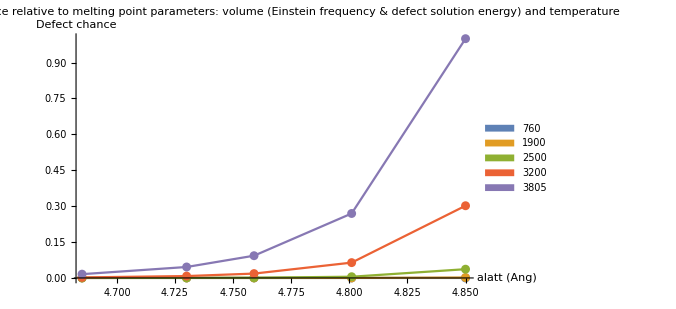

```mathematica
Plot relative hop rates;
(*Define relative hopping rate*)
relativeHopping[vol_,temp_]:=vineyard[Esol[[i]],temps[[j]]][[i]]/vineyard[Esol[[5]],temps[[5]]][[5]]
(*plot relative hopping rate vs alatt*)
plotInfo={PlotRange->All, ImageSize->500,PlotLabel->"Defect chance relative to melting point parameters: \nvolume (Einstein frequency & defect solution energy) and temperature",AxesLabel->{"alatt (Ang)","Defect chance"}};
joined=ListPlot[Table[Table[{alatts[[i]],relativeHopping[i,j]},{i,1,5}],{j,1,5}],plotInfo,PlotLegends->SwatchLegend[temps],Joined->True];
notjoined=ListPlot[Table[Table[{alatts[[i]],relativeHopping[i,j]},{i,1,5}],{j,1,5}],plotInfo];
a=Show[joined,notjoined]
```

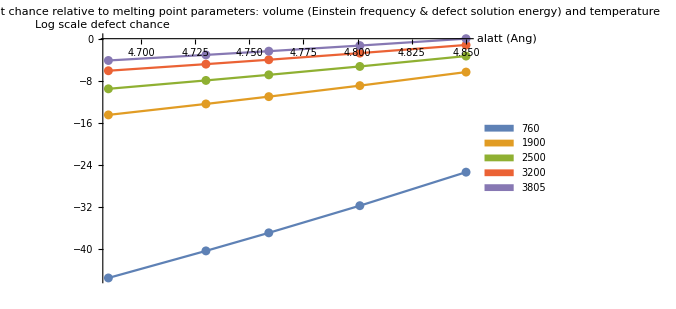

```mathematica
(*Prep data for a log plot of relative hopping rates*)
joinedLog=ListPlot[Table[Table[{alatts[[i]],Log@relativeHopping[i,j]},{i,1,5}],{j,1,5}],Joined->True,PlotRange->All,PlotLegends->SwatchLegend[temps]];
notjoinedLog=ListPlot[Table[Table[{alatts[[i]],Log@relativeHopping[i,j]},{i,1,5}],{j,1,5}],PlotRange->All];
plotInfoLog={ImageSize->500,PlotLabel->"Log scale defect chance relative to melting point parameters: \nvolume (Einstein frequency & defect solution energy) and temperature",AxesLabel->{"alatt (Ang)","Log scale defect chance"}};

b=Show[joinedLog,notjoinedLog,plotInfoLog]
```

```mathematica
GraphicsGrid[{{a,b}},ImageSize->1200]
```

-Graphics-

```mathematica
(Log[32]+Log[192])//N
0.125*Log[32*192]//N
(Log[4]+Log[24])//N
```

8.72323

1.0904

4.56435

```mathematica
Sdefectconfig[Ncations_,Nvac_,Ninterstit_,Ninterstitsites_]:=K2meV*(Log[Ncations!/((Ncations-Nvac)!*Nvac!)]+Log[Ninterstitsites!/((Ninterstitsites-Ninterstit)!*Ninterstit!)])
```

```mathematica
Esol[[5]]
S1frenkeldefect[T_]:=kB*(Log[32]+Log[192])*T
```

2077.54

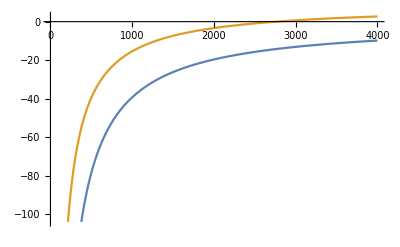

```mathematica
Plot[Evaluate@Log@{arrhenius[Esol[[1]],T],arrhenius[Esol[[5]]-S1frenkeldefect[T],T]},{T,1,4000}]
```

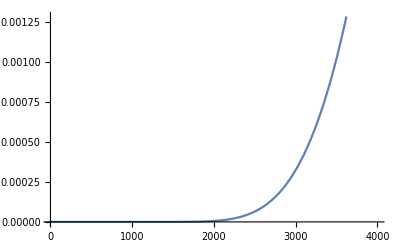

```mathematica
Plot[{arrhenius[Esol[[5]],T]},{T,1,4000}]
```

```mathematica
arrhenius[Esol
```

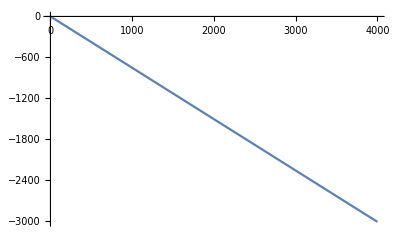

```mathematica
(*Frenkel entropy contribution *)
Plot[-kB*(Log[32]+Log[192])*T,{T,1,4000}]
```

```mathematica
(*Defect concentration*)
(* http://www.tf.uni-kiel.de/matwis/amat/def_en/kap_2/backbone/r2_1_2.html *)
(*conc = (root defect interstitial sites over root number of anions)*Exp[entropy/2K]*Exp[H/2K*T]*)
```

```mathematica
Esol/1000
```

{3.38458,3.05035,2.82737,2.49198,2.07754}

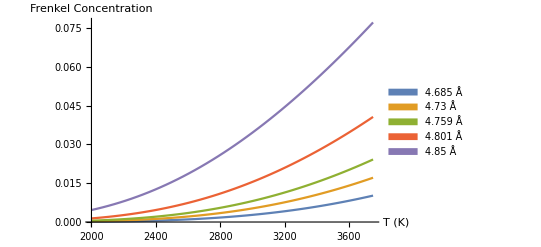

```mathematica
Conc[T_]:=(Sqrt[192]/Sqrt[32])*Exp[(kB*(Log[32]+Log[192]))/(2kB)]*Exp[-Esol/(2*kB*T)]
Conc2[T_]:=Exp[-Esol/(kB*T)]
defectinfo={AxesLabel->{"T (K)","Frenkel\nConcentration"},PlotLegends->SwatchLegend[{SetPrecision[alatts,4]  Å}],PlotStyle->"Thick"};
Plot[Evaluate[0.01Conc[T]],{T,2000,3750},Evaluate@defectinfo]
```

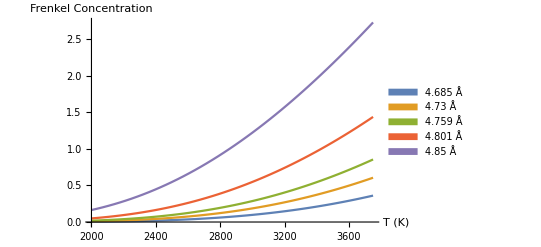

```mathematica
Conc[T_]:=(Sqrt[192]/Sqrt[32])*Exp[(kB*(Log[32]+Log[24]))/(2kB)]*Exp[-Esol/(2*kB*T)]
Conc2[T_]:=Exp[-Esol/(kB*T)]
Conc3[T_]:=(Sqrt[24]/Sqrt[32])*Exp[(kB*(Log[32]+Log[24]))/(2kB)]*Exp[-Esol/(2*kB*T)]
defectinfo={AxesLabel->{"T (K)","Frenkel\nConcentration"},PlotLegends->SwatchLegend[{SetPrecision[alatts,4]  Å}],PlotStyle->"Thick"};
Plot[Evaluate[Conc[T]],{T,2000,3750},Evaluate@defectinfo]
```

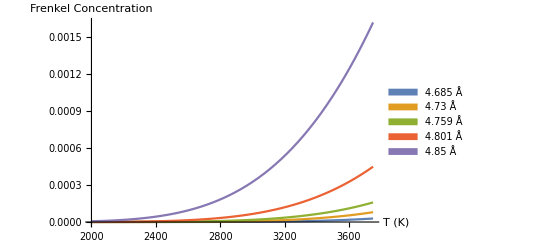

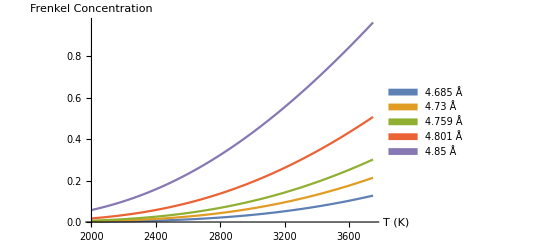

```mathematica
Plot[{Evaluate@Conc2[T]},{T,2000,3750},Evaluate@defectinfo,PlotRange->All]
Plot[{Evaluate@Conc3[T]},{T,2000,3750},Evaluate@defectinfo]
```

```mathematica
Esol
```

{3384.58,3050.35,2827.37,2491.98,2077.54}

```mathematica
Exp[-2077.5399999998854/(kB*3800)]
```

0.00175649

```mathematica
(Sqrt[24]/Sqrt[32])*Exp[(kB*(Log[32]+Log[24]))/(2kB)]
(Sqrt[192]/Sqrt[32])*Exp[(kB*(Log[32]+Log[192]))/(2kB)]
```

24.

192.

```mathematica
Exp[-2/(3800*8.6173324*10^−5)]
```

0.00222579

```mathematica
3
```